https://royvanrijn.com/blog/2019/05/sat-solving-part-one/

```mathematica
1+1
```

2

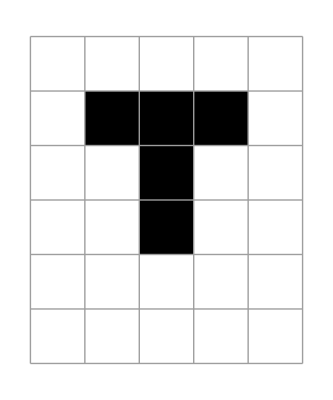
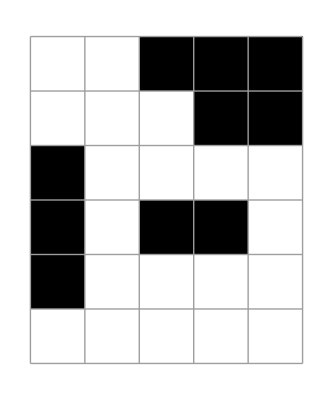
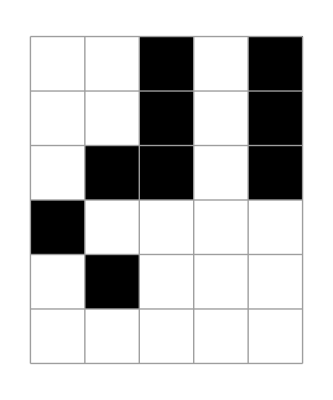
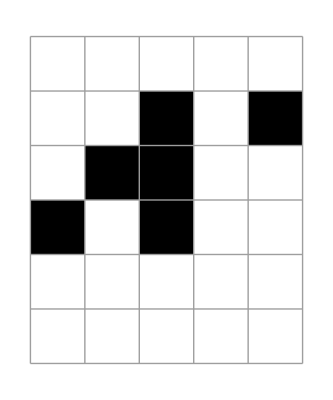
{112.263,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/00_still_life_stack_question/001_counting_function/countModule5.m"];
LIFE=({{0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPAay]*)
AbsoluteTiming[{LIFE//plt,updateIJ[LIFE]//lifePlot}]
```

```mathematica
formulaIJ=(and@{Nothing,(x2[##]&&count[{2,3},{##},x2])~bs~xp[##],(x2[##]&&!count[{2,3},{##},x2])~bs~!xp[##]
(*not*),(!x2[##]&&count[{3},{##},x2])~bs~xp[##],(!x2[##]&&!count[{3},{##},x2])~bs~!xp[##],(x1[##]&&count[{2,3},{##},x1])~bs~x2[##],(x1[##]&&count[{2,3},{##},x1])~bs~!x2[##]
(*not*),(!x1[##]&&count[{3},{##},x1])~bs~x2[##],(!x1[##]&&!count[{3},{##},x1])~bs~!x2[##],(x0[##]&&count[{2,3},{##},x0])~bs~x1[##],(x0[##]&&!count[{2,3},{##},x0])~bs~!x1[##],(!x0[##]&&count[{3},{##},x0])~bs~x1[##],(!x0[##]&&!count[{3},{##},x0])~bs~!x1[##]})&;
formulaIJ[1,1]
```

(!x2[1,1]||!x2[1,2]||!x2[2,1]||xp[1,1])&&(!x2[1,1]||!x2[1,2]||!x2[2,2]||xp[1,1])&&(!x2[1,1]||!x2[2,1]||!x2[2,2]||xp[1,1])&&(x2[1,1]||!xp[1,1])&&(x2[1,2]||x2[2,1]||!xp[1,1])&&(x2[1,2]||x2[2,2]||!xp[1,1])&&(x2[2,1]||x2[2,2]||!xp[1,1])&&(!x2[1,1]||x2[1,2]||x2[2,1]||!xp[1,1])&&(!x2[1,1]||x2[1,2]||x2[2,2]||!xp[1,1])&&(!x2[1,1]||x2[2,1]||x2[2,2]||!xp[1,1])&&(x2[1,1]||xp[1,1])&&(!x2[1,2]||!x2[2,1]||xp[1,1])&&(!x2[1,2]||!x2[2,2]||xp[1,1])&&(!x2[2,1]||!x2[2,2]||xp[1,1])&&(!x2[1,1]||!xp[1,1])&&(x2[1,1]||!x2[1,2]||!x2[2,1]||!x2[2,2]||xp[1,1])&&(x2[1,2]||!xp[1,1])&&(x2[2,1]||!xp[1,1])&&(x2[2,2]||!xp[1,1])&&(!x2[1,1]||xp[1,1])&&(x2[1,1]||x2[1,2]||!xp[1,1])&&(x2[1,1]||x2[2,1]||!xp[1,1])&&(x2[1,1]||x2[2,2]||!xp[1,1])&&(!x2[1,2]||!x2[2,1]||!x2[2,2]||xp[1,1])&&(!x1[1,1]||!x1[1,2]||!x1[2,1]||x2[1,1])&&(!x1[1,1]||!x1[1,2]||!x1[2,2]||x2[1,1])&&(!x1[1,1]||!x1[2,1]||!x1[2,2]||x2[1,1])&&(x1[1,1]||!x2[1,1])&&(x1[1,2]||x1[2,1]||!x2[1,1])&&(x1[1,2]||x1[2,2]||!x2[1,1])&&(x1[2,1]||x1[2,2]||!x2[1,1])&&(!x1[1,1]||!x1[1,2]||!x1[2,1]||!x2[1,1])&&(!x1[1,1]||!x1[1,2]||!x1[2,2]||!x2[1,1])&&(!x1[1,1]||!x1[2,1]||!x1[2,2]||!x2[1,1])&&(x1[1,1]||x2[1,1])&&(x1[1,2]||x1[2,1]||x2[1,1])&&(x1[1,2]||x1[2,2]||x2[1,1])&&(x1[2,1]||x1[2,2]||x2[1,1])&&(!x1[1,1]||!x2[1,1])&&(x1[1,1]||!x1[1,2]||!x1[2,1]||!x1[2,2]||x2[1,1])&&(x1[1,2]||!x2[1,1])&&(x1[2,1]||!x2[1,1])&&(x1[2,2]||!x2[1,1])&&(!x1[1,1]||x2[1,1])&&(x1[1,1]||x1[1,2]||!x2[1,1])&&(x1[1,1]||x1[2,1]||!x2[1,1])&&(x1[1,1]||x1[2,2]||!x2[1,1])&&(!x1[1,2]||!x1[2,1]||!x1[2,2]||x2[1,1])&&(!x0[1,1]||!x0[1,2]||!x0[2,1]||x1[1,1])&&(!x0[1,1]||!x0[1,2]||!x0[2,2]||x1[1,1])&&(!x0[1,1]||!x0[2,1]||!x0[2,2]||x1[1,1])&&(x0[1,1]||!x1[1,1])&&(x0[1,2]||x0[2,1]||!x1[1,1])&&(x0[1,2]||x0[2,2]||!x1[1,1])&&(x0[2,1]||x0[2,2]||!x1[1,1])&&(!x0[1,1]||x0[1,2]||x0[2,1]||!x1[1,1])&&(!x0[1,1]||x0[1,2]||x0[2,2]||!x1[1,1])&&(!x0[1,1]||x0[2,1]||x0[2,2]||!x1[1,1])&&(x0[1,1]||x1[1,1])&&(!x0[1,2]||!x0[2,1]||x1[1,1])&&(!x0[1,2]||!x0[2,2]||x1[1,1])&&(!x0[2,1]||!x0[2,2]||x1[1,1])&&(!x0[1,1]||!x1[1,1])&&(x0[1,1]||!x0[1,2]||!x0[2,1]||!x0[2,2]||x1[1,1])&&(x0[1,2]||!x1[1,1])&&(x0[2,1]||!x1[1,1])&&(x0[2,2]||!x1[1,1])&&(!x0[1,1]||x1[1,1])&&(x0[1,1]||x0[1,2]||!x1[1,1])&&(x0[1,1]||x0[2,1]||!x1[1,1])&&(x0[1,1]||x0[2,2]||!x1[1,1])&&(!x0[1,2]||!x0[2,1]||!x0[2,2]||x1[1,1])